0.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {676.77}. NIntegrate obtained 2.31974 and 0.000198888 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {676.77}. NIntegrate obtained 2.31899 and 0.000191723 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {676.77}. NIntegrate obtained 2.31543 and 0.000184117 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

0.0005

0.001

0.0015

0.002

0.0025

0.003

0.0035

0.004

0.0045

0.005

{0.,0.0005,0.001,0.0015,0.002,0.0025,0.003,0.0035,0.004,0.0045,0.005}

Transpose[{{0.,0.0005,0.001,0.0015,0.002,0.0025,0.003,0.0035,0.004,0.0045,0.005},{0.0398666}}]

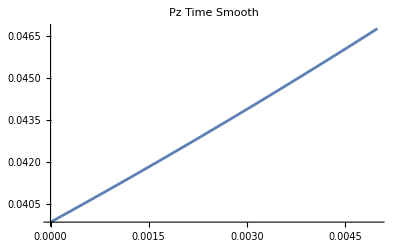

Offsets_m_15_a_5.0.mat

InterpolatingFunction::dmval: Input value {0.0051} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0052} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0053} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

PzStatic_m_15_a_5.0.mat

InterpolatingFunction::dmval: Input value {0.0051} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0052} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0053} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

PxStatic_m_15_a_5.0.mat

InterpolatingFunction::dmval: Input value {0.0051} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0052} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0053} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

PzTime_m_15_a_5.0.mat

InterpolatingFunction::dmval: Input value {0.0051} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0052} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0053} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

PxTime_m_15_a_5.0.mat

Export::type: MaxXoffset/100 cannot be exported to the MAT format.

Offsets_m_14_a_19.15.mat

Export::type: funPzStat[0] cannot be exported to the MAT format.

PzStatic_m_14_a_19.15.mat

Export::type: funPzStat'[0]/(6000000000 π) cannot be exported to the MAT format.

PxStatic_m_14_a_19.15.mat

Export::type: InterpolatingFunction[{{0.,0.01915}},{5,7,0,{11},{4},0,0,0,0,Automatic,«3»},{{0.,0.001915,0.00383,0.005745,0.00766,0.009575,0.01149,0.013405,0.01532,0.017235,«1»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«2»},{0.0398666,0.0412694,0.0427157,0.0442055,0.0457388,0.0473157,0.0489361,0.0506001,0.0523076,0.0540586,«1»}},{Automatic}][MaxXoffset/100] cannot be exported to the MAT format.

PzTime_m_14_a_19.15.mat

Export::type: (InterpolatingFunction[{{0.,0.01915}},{5,7,0,{11},{4},{1},0,0,0,Automatic,«3»},{{0.,0.001915,0.00383,«5»,0.01532,0.017235,«1»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«2»},{0.0398666,0.0412694,0.0427157,0.0442055,0.0457388,0.0473157,0.0489361,0.0506001,0.0523076,0.0540586,«1»}},{Automatic}][(«10»)/100])/(6000000000 π) cannot be exported to the MAT format.

PxTime_m_14_a_19.15.mat

```mathematica
M = 15; (*Azimuthal order - change this to see r^m variation*)

a = 0.01; (*beam pipe radius*)
Eg0 = 1;
Eg1 = 0.3464;
Eg2 = 0.0546;

a = 0.01/2; (*beam pipe radius*)
Eg0 = 1;
Eg1 = 0.1605;
Eg2 = 0.0125;

c = 299792458; (*Speed of light*)

(*Parameters to define the cavity*)
frf = 3*10^9; (*freq [Hz]*)
Lpipe = 0.25; (*length of pipe either side [m]*)
g = c/frf/2; (*total cavity length [m]*)

aMax = 0.0383; (*total cavity radius*)


(*Parameters to define numerical steps*)
NzSteps = 1000;  (*Default = 1000*)
Noffsets = 10; (* Default = 10*)
NkSteps = 1000; (*Default = 1000*)
UpperkFactor = 5000; (*Default = 5000*)
LSpacing = 500; (*How many longitudinal points to output*)

(*derived parameters*)
kl = 2*Pi*frf/c; 
L = g/2 + Lpipe;
z = N@Subdivide[-L,L,NzSteps];

DeltaPzStat = {};
DeltaPzTime = {};

(*Determine limits for integral - do the integrals separately for J_m and I_m*)
kspecial = Pi/g/2;
klower1 = 0;
kupper1 = kl;
klower2 =kl;
kupper2 = UpperkFactor*klower2;
krange1 = N@Subdivide[klower1,kupper1,NkSteps]; (*determine the r values at which to calculate the integral*)
krange2 = N@Subdivide[klower2,kupper2,UpperkFactor*NkSteps]; (*determine the r values at which to calculate the integral*)

roffset = N@Subdivide[0,a,Noffsets]; (*determine the r values at which to calculate the integral*)

Export[StringTemplate["Z_m_`1`_a_`2`.mat"][M,a*1000], Table[z,{z,-L,L,L/LSpacing}],"MAT"];

(*loop through the different radius values*)
For[i=0,i<Length[roffset],i++,

r = roffset[[i+1]];
Print[r];

(*do the integral in two parts*)
EzJ = g/Pi*NIntegrate[Sinc[k*g/2]*(Eg0*BesselJ[0,√(kl^2-k^2)*r]/BesselJ[0,√(kl^2-k^2)*a]+Eg1*BesselJ[1,√(kl^2-k^2)*r]/BesselJ[1,√(kl^2-k^2)*a]+Eg2*BesselJ[2,√(kl^2-k^2)*r]/BesselJ[2,√(kl^2-k^2)*a])*Cos[k*z],{k,klower1,kupper1}];
EzI = g/Pi*NIntegrate[Sinc[k*g/2]*(Eg0*BesselI[0,√(k^2-kl^2)*r]/BesselI[0,√(k^2-kl^2)*a]+Eg1*BesselI[1,√(k^2-kl^2)*r]/BesselI[1,√(k^2-kl^2)*a]+Eg2*BesselI[2,√(k^2-kl^2)*r]/BesselI[2,√(k^2-kl^2)*a])*Cos[k*z],{k,klower2,kupper2}];
EzT = (EzJ+EzI);

(*Collect the z and Ez data together*)
dataT=Transpose@{z,EzT};
dataJ=Transpose@{z,EzJ};
  dataI=Transpose@{z,EzI};

(*Include the klz variation*)
TimeArray = Cos[kl*z];
dataTTime = Transpose@{z,EzT*TimeArray};

funStat = Interpolation[dataT]; 
AppendTo[DeltaPzStat, NIntegrate[funStat[z],{z,-L,L}]];

(*interpolate on the uncollected values*)
funTime = Interpolation[dataTTime]; 
(*undertake the second integration*)
AppendTo[DeltaPzTime, NIntegrate[funTime[z],{z,-L,L}]];

SetDirectory[FileNameJoin[{NotebookDirectory[], "/Outputs"}]];
Export[StringTemplate["Ez_m_`1`_a_`2`_r_`3`.mat"][M,a*1000,r*1000], Table[funStat[z],{z,-L,L,L/LSpacing}],"MAT"];

(*Make plots to visualise*)
Plot[funTime[z],{z,-L,L},AxesLabel->{"z [m]","Ez(t)"},PlotRange->Full]
ListLinePlot[{dataTTime, dataT,dataJ,dataI},AxesLabel->{"z [m]","E_z [V/m]"}, PlotLegends ->{"E_z(t)","E_z","E_z (k<k_rf)","E_z (k>k_rf)" },GridLines->Automatic,PlotLabel-> StringTemplate["a = `1` [mm]; r = `2` [mm]"][a*1000,r*1000],PlotRange->Full,Epilog->{Directive[AbsoluteThickness[2],Black],{InfiniteLine[{g/2, g/2},{0,1}],InfiniteLine[{-g/2, -g/2},{0,1}]}}]
]
Print[roffset]
Print[dataPzTime]

(*Plot the f(r) as a function of r*)
dataPzStat=Transpose@{roffset,DeltaPzStat};
dataPzTime = Transpose@{roffset,DeltaPzTime};
funPzStat = Interpolation[dataPzStat];
funPzTime = Interpolation[dataPzTime];

Plot[funPzTime[roffset],{roffset,0,a},PlotLabel->"Pz Time Smooth"]

SetDirectory[FileNameJoin[{NotebookDirectory[], "/Outputs"}]];
Export[StringTemplate["Offsets_m_`1`_a_`2`.mat"][M,a*1000], Table[roffset,{roffset,0,MaxXoffset,MaxXoffset/100}],"MAT"]
Export[StringTemplate["PzStatic_m_`1`_a_`2`.mat"][M,a*1000], Table[funPzStat[roffset],{roffset,0,MaxXoffset,MaxXoffset/100}],"MAT"]
Export[StringTemplate["PxStatic_m_`1`_a_`2`.mat"][M,a*1000], Table[funPzStat'[roffset]/(2*Pi*frf),{roffset,0,MaxXoffset,MaxXoffset/100}],"MAT"]
Export[StringTemplate["PzTime_m_`1`_a_`2`.mat"][M,a*1000], Table[funPzTime[roffset],{roffset,0,MaxXoffset,MaxXoffset/100}],"MAT"]
Export[StringTemplate["PxTime_m_`1`_a_`2`.mat"][M,a*1000], Table[funPzTime'[roffset]/(2*Pi*frf),{roffset,0,MaxXoffset,MaxXoffset/100}],"MAT"]
```